```mathematica
link=Install[LinkConnect[" 40505@192.168.150.128,42649@192.168.150.128",LinkProtocol->"TCPIP"]]
```

LinkObject[…]

```mathematica
handle = With[
{c=15,Ωp=1.0,ΩO=1/16,Ωe=-100,θr=0.45,θe=Sqrt[0.8],θbp=0.045,θbO=0.01125,ωbp=15*Sqrt[0.45],ωbO=3.75*Sqrt[0.45],ωe=150,
ωp ={0.039893,0.143882,0.348679,0.597894,0.815419,0.984766,1.11653,1.21888,1.29599,1.34998,1.38201,1.39263,1.38201,1.34998,1.29599,1.21888,1.11653,0.984766,0.815419,0.597894,0.348679,0.143882,0.039893},
vd={1.90288,1.99424,2.025,1.99424,1.90288,1.7537,1.55124,1.30164,1.0125,0.692591,0.351638,0,-0.351638,-0.692591,-1.0125,-1.30164,-1.55124,-1.7537,-1.90288,-1.99424,-2.025,-1.99424,-1.90288},
vr={-0.692591,-0.351638,0,0.351638,0.692591,1.0125,1.30164,1.55124,1.7537,1.90288,1.99424,2.025,1.99424,1.90288,1.7537,1.55124,1.30164,1.0125,0.692591,0.351638,0,-0.351638,-0.692591}
},
dist=Join[
Thread[wstpDRingDistribution[Ωp,ωp,θr,θr,vd,vr]],
Thread[wstpDMaxwellianDistribution[{Ωp,Ωe,ΩO},{ωbp,ωe,ωbO},{θbp,θe,θbO}]]];
wstpDCreateDispersionObject[c,dist]];
```

```mathematica
check=With[{k=6.5,wna=88Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[3.8,0.02] (1+0.0001 I {0,1,2}),MaxIterations->100]];
```

```mathematica
sol=With[{k=Range[0.5,1.3,0.01],wna=88Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[0.65,-0.00001] (1+0.0001 I {0,1,2}),MaxIterations->100]];


ListLinePlot[Im[sol[[2,2]]]]
```

```mathematica
gama={};
with[{k=Range[81]},gama=Append[gama,Im[sol[[2,2,k]]]]];
Export["1.txt",gama];
```

{3.67332-0.067381 ⅈ,3.66984-0.0625339 ⅈ,3.66569-0.0642593 ⅈ,3.66189-0.062192 ⅈ,3.65811-0.059679 ⅈ,3.65433-0.0565938 ⅈ,3.65059-0.0527841 ⅈ,3.64699-0.0480338 ⅈ,3.64375-0.042045 ⅈ,3.64666-0.0214286 ⅈ,3.6494-0.0112541 ⅈ,3.64279-0.0148101 ⅈ,3.64821-0.0047603 ⅈ,3.66942+0.0110728 ⅈ,3.68049+0.0163292 ⅈ,3.67687+0.0156639 ⅈ,3.68856+0.0192385 ⅈ,3.7009+0.0215229 ⅈ,3.7357+0.0237417 ⅈ,3.75034+0.0229681 ⅈ,3.76539+0.0216356 ⅈ}

{3.67332-0.067381 ⅈ,3.66984-0.0625339 ⅈ,3.66569-0.0642593 ⅈ,3.66189-0.062192 ⅈ,3.65811-0.059679 ⅈ,3.65433-0.0565938 ⅈ,3.65059-0.0527841 ⅈ,3.64699-0.0480338 ⅈ,3.64375-0.042045 ⅈ,3.64666-0.0214286 ⅈ,3.6494-0.0112541 ⅈ,3.64279-0.0148101 ⅈ,3.64821-0.0047603 ⅈ,3.66942+0.0110728 ⅈ,3.68049+0.0163292 ⅈ,3.67687+0.0156639 ⅈ,3.68856+0.0192385 ⅈ,3.7009+0.0215229 ⅈ,3.7357+0.0237417 ⅈ,3.75034+0.0229681 ⅈ,3.76539+0.0216356 ⅈ,3.77494+0.0204286 ⅈ,3.77181+0.0197431 ⅈ,3.80746+0.0168046 ⅈ,3.82507+0.0151502 ⅈ,3.82173+0.0147269 ⅈ,3.83911+0.0133624 ⅈ,3.85663+0.012229 ⅈ,3.87419+0.0113071 ⅈ,3.89171+0.0105619 ⅈ,3.90915+0.0099575 ⅈ,3.92647+0.00946091 ⅈ,3.94363+0.00903907 ⅈ,3.96057+0.00863609 ⅈ,3.97713+0.00799873 ⅈ,4.01058+0.00681609 ⅈ,4.03443+0.00815785 ⅈ,4.0511+0.00823891 ⅈ,4.06773+0.00826531 ⅈ,4.08423+0.00830124 ⅈ,4.07824+0.00793571 ⅈ}

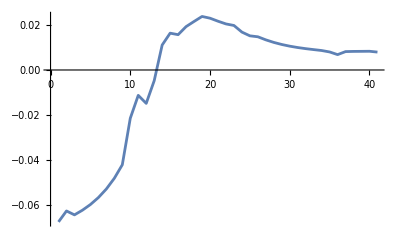

```mathematica
sol1=With[{k=Range[6.5,5.5,-0.05],wna=88Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[3.8,0.02] (1+0.0001 I {0,1,2}),MaxIterations->100]];
sol2=With[{k=Range[6.55,7.5,0.05],wna=88Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[3.8,0.02] (1+0.0001 I {0,1,2}),MaxIterations->100]];
sol1=Reverse[sol1[[2,2]]]
sol=Join[sol1,sol2[[2,2]]]
ListLinePlot[Im[sol]]
```

```mathematica
Export["88oim-4,5.5-7.5.csv",Im[sol]];

Export["88ore-4,5.5-7.5.csv",Re[sol]];
```